```mathematica
a=Import["G:\\calc-online\\gpd\\k-result\\diagram-k-q-n.wdx"];
```

```mathematica
f1=Query[1,1]@a;
g1=Query[1,2]@a;
f2=Query[2,1]@a;
g2=Query[2,2]@a;
nf1=f1/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.1,Q^2->1,q3->0.97710345,Λ->1};
ng1=g1/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.1,Q^2->1,q3->0.97710345,Λ->1};
nf2=f2/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.1,Q^2->1,q3->0.97710345,Λ->1};
ng2=g2/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.1,Q^2->1,q3->0.97710345,Λ->1};
```

```mathematica
b1=f1/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.2,Q^2->1,q3->0.90494455,Λ->1};
b2=g1/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.2,Q^2->1,q3->0.90494455,Λ->1};
b3=f2/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.2,Q^2->1,q3->0.90494455,Λ->1};
b4=g2/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.2,Q^2->1,q3->0.90494455,Λ->1};
```

```mathematica
NIntegrate[ng1,{k3,0,∞},{θ,0,2π},{y,-0.1,0.1},WorkingPrecision->10]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -2.58166061651729980626215206676473616614501143515767703711131×10^-10 ⅈ and 4.58636466827373013003675516428462423794355250430621786537044×10^-9 for the integral and error estimates.

-2.581660617×10^-10 ⅈ

```mathematica
NIntegrate[nf1,{k3,0,∞},{θ,0,2π},{y,-0.1,0.1},WorkingPrecision->10]
```

-1.308302283 ⅈ

```mathematica
Simplify[ng1]
```

((0.+7.74863×10^-12 ⅈ) k3 y (-5.74704×10^11-1.36053×10^13 y+4.51307×10^12 y^2+2.38454×10^15 y^3+1.61898×10^16 y^4-6.84396×10^16 y^5-1.07462×10^18 y^6-3.42713×10^18 y^7-1.46913×10^18 y^8+3.09728×10^18 y^9-9.03446×10^17 y^10+7.19639×10^16 y^11-3.83156 y^12+0.48169 y^13+k3^12 (0.00827392+0.231739 y+1.894 y^2+4.14 y^3+1. y^4)+k3^10 (0.065536+1.04464 y+9.11475 y^2+60.1122 y^3+79.779 y^4+8.13428 y^5-3.39516 y^6)+k3^8 (0.00524288+3.26288 y^2+78.6818 y^3+596.914 y^4+269.43 y^5-31.2545 y^6-32.1234 y^7+3.84238 y^8)+k3^6 (-4.96474×10^11-4.96474×10^12 y+9.92948×10^13 y^2+9.92948×10^14 y^3-4.96474×10^15 y^4-4.96474×10^16 y^5-1836.29 y^6+128.683 y^7-35.0814 y^8+17.4507 y^9-1.4495 y^10)+k3^4 (-1.56794×10^12-2.27894×10^13 y+2.44173×10^14 y^2+4.57473×10^15 y^3-1.79651×10^15 y^4-2.31265×10^17 y^5-6.94143×10^17 y^6+1.68561×10^17 y^7+2427.09 y^8-44.3541 y^9-40.2785 y^10+2.81203 y^11)+k3^2 (-1.64617×10^12-3.14313×10^13 y+1.53127×10^14 y^2+6.03824×10^15 y^3+1.89187×10^16 y^4-2.64729×10^17 y^5-1.79287×10^18 y^6-2.47633×10^18 y^7+1.59023×10^18 y^8-1.90764×10^17 y^9+290.282 y^10-34.0994 y^11+1.43138 y^12)+k3 (-2.78482×10^12-6.28811×10^13 y+1.25901×10^13 y^2+1.05762×10^16 y^3+7.88239×10^16 y^4-2.27285×10^17 y^5-5.00338×10^18 y^6-2.03038×10^19 y^7-2.19899×10^19 y^8+1.51654×10^19 y^9-1.84923×10^18 y^10+331.371 y^11+0.209715 y^12+k3^10 (0.0648806+1.69738 y+17.8377 y^2+85.6626 y^3+124.368 y^4+29.3131 y^5)+k3^8 (0.267387+2.71581 y+33.8061 y^2+495.075 y^3+1746.25 y^4+1355.69 y^5+133.098 y^6-66.3485 y^7)+k3^6 (-1.01622×10^12+2.95057 y+2.03243×10^14 y^2+188.836 y^3-1.01622×10^16 y^4+7667.51 y^5-2111.94 y^6-205.271 y^7-245.459 y^8+37.544 y^9)+k3^4 (-4.66468×10^12-4.36596×10^13 y+7.90854×10^14 y^2+8.73192×10^15 y^3-1.82304×10^16 y^4-4.36596×10^17 y^5-1.42082×10^18 y^6-30271. y^7+5102.35 y^8+462.243 y^9-72.9513 y^10)+k3^2 (-6.43356×10^12-1.05817×10^14 y+6.51651×10^14 y^2+1.98727×10^16 y^3+6.3002×10^16 y^4-8.00042×10^17 y^5-6.4157×10^18 y^6-1.29062×10^19 y^7+3.25499×10^18 y^8-5485.63 y^9+722.944 y^10-37.1907 y^11)) Cos[θ]+k3^2 (-4.78929×10^12-1.14559×10^14 y-4.54768×10^13 y^2+1.89307×10^16 y^3+1.46787×10^17 y^4-3.47793×10^17 y^5-8.83589×10^18 y^6-4.01257×10^19 y^7-5.98729×10^19 y^8+1.57115×10^19 y^9-2627.65 y^10+164.417 y^11+k3^8 (0.132383+3.40001 y+54.3162 y^2+454.841 y^3+1314.64 y^4+1245.41 y^5+286.419 y^6)+k3^6 (1.04858+2.18104 y-83.0472 y^2+401.982 y^3+5395.89 y^4+14100.3 y^5+3433.58 y^6+336.032 y^7-324.147 y^8)+k3^4 (-2.97885×10^12-2.97885×10^13 y+5.95769×10^14 y^2+5.95769×10^15 y^3-2.97885×10^16 y^4-2.97885×10^17 y^5-4210.66 y^6-43731.1 y^7+1266.72 y^8+631.848 y^9)+k3^2 (-7.69375×10^12-1.33817×10^14 y+8.34493×10^14 y^2+2.54089×10^16 y^3+6.39139×10^16 y^4-1.06726×10^18 y^5-7.04257×10^18 y^6-1.35457×10^19 y^7+43965.4 y^8-5313.5 y^9+317.242 y^10)) Cos[θ]^2+k3^3 (-3.52722×10^12-9.37017×10^13 y-1.53445×10^14 y^2+1.55642×10^16 y^3+1.32204×10^17 y^4-3.01788×10^17 y^5-7.72848×10^18 y^6-3.17614×10^19 y^7-4.30206×10^19 y^8+10765.6 y^9+1355.6 y^10+k3^6 (0.132383+1.32383 y+100.663 y^2+1276.41 y^3+3480.49 y^4+8234.32 y^5+4164.86 y^6+932.871 y^7)+k3^4 (-0.256901-2.40124 y+135.895 y^2+1884.42 y^3+7043.75 y^4+18373.1 y^5+19458.7 y^6-21553.1 y^7-1835.7 y^8)+k3^2 (-2.91064×10^12-5.82128×10^13 y+2.91064×10^14 y^2+1.16426×10^16 y^3+2.91064×10^16 y^4-5.82128×10^17 y^5-2.91064×10^18 y^6-173548. y^7+22697.2 y^8-795.464 y^9)) Cos[θ]^3+k3^4 (-9.47999×10^11-2.844×10^13 y-9.47999×10^13 y^2+4.73999×10^15 y^3+4.73999×10^16 y^4-9.47999×10^16 y^5-2.844×10^18 y^6-9.47999×10^18 y^7+10195.2 y^8-5422.4 y^9+k3^4 (0.00065536+4.20086 y+109.052 y^2+939.524 y^3+3763.47 y^4+12588.2 y^5+17978.7 y^6+74.6297 y^7)+k3^2 (0.00065536+0.0484966 y-66.0183 y^2-124.822 y^3+7532.3 y^4+26693.2 y^5+47463.8 y^6-58061.6 y^7-1234.92 y^8)) Cos[θ]^4+k3^5 (-0.0122829+(-0.727071+1.04858 k3^2) y+(-18.5624+18.9583 k3^2) y^2+(-250.4+150.492 k3^2) y^3+(-2021.07+1726.04 k3^2) y^4+(-9801.92+11757.5 k3^2) y^5+(-22723.1+11114.3 k3^2) y^6+(-16632.3+3768.8 k3^2) y^7-5261.33 y^8) Cos[θ]^5+k3^6 (-0.000384-0.0448 y-1.19603 y^2-12.0586 y^3-25.1658 y^4+301.99 y^5+1342.18 y^6) Cos[θ]^6))/((0.998219+1. k3^2-0.130986 y-1.13172 y^2+k3 (0.977103+9.77103 y) Cos[θ])^2 (0.507754+1. k3^2+4.77366 y-1.13172 y^2+k3 (0.977103+9.77103 y) Cos[θ]) (1.48868+1. k3^2+4.77366 y-1.13172 y^2+k3 (0.977103+9.77103 y) Cos[θ])^3 (0.998219+1. k3^2+9.6783 y-1.13172 y^2+k3 (0.977103+9.77103 y) Cos[θ])^2)

```mathematica
Cancel[%12]
```

((0.+7.74863×10^-12 ⅈ) k3 y (-5.74704×10^11-1.64617×10^12 k3^2-1.56794×10^12 k3^4-4.96474×10^11 k3^6+0.00524288 k3^8+0.065536 k3^10+0.00827392 k3^12-1.36053×10^13 y-3.14313×10^13 k3^2 y-2.27894×10^13 k3^4 y-4.96474×10^12 k3^6 y+1.04464 k3^10 y+0.231739 k3^12 y+4.51307×10^12 y^2+1.53127×10^14 k3^2 y^2+2.44173×10^14 k3^4 y^2+9.92948×10^13 k3^6 y^2+3.26288 k3^8 y^2+9.11475 k3^10 y^2+1.894 k3^12 y^2+2.38454×10^15 y^3+6.03824×10^15 k3^2 y^3+4.57473×10^15 k3^4 y^3+9.92948×10^14 k3^6 y^3+78.6818 k3^8 y^3+60.1122 k3^10 y^3+4.14 k3^12 y^3+1.61898×10^16 y^4+1.89187×10^16 k3^2 y^4-1.79651×10^15 k3^4 y^4-4.96474×10^15 k3^6 y^4+596.914 k3^8 y^4+79.779 k3^10 y^4+1. k3^12 y^4-6.84396×10^16 y^5-2.64729×10^17 k3^2 y^5-2.31265×10^17 k3^4 y^5-4.96474×10^16 k3^6 y^5+269.43 k3^8 y^5+8.13428 k3^10 y^5-1.07462×10^18 y^6-1.79287×10^18 k3^2 y^6-6.94143×10^17 k3^4 y^6-1836.29 k3^6 y^6-31.2545 k3^8 y^6-3.39516 k3^10 y^6-3.42713×10^18 y^7-2.47633×10^18 k3^2 y^7+1.68561×10^17 k3^4 y^7+128.683 k3^6 y^7-32.1234 k3^8 y^7-1.46913×10^18 y^8+1.59023×10^18 k3^2 y^8+2427.09 k3^4 y^8-35.0814 k3^6 y^8+3.84238 k3^8 y^8+3.09728×10^18 y^9-1.90764×10^17 k3^2 y^9-44.3541 k3^4 y^9+17.4507 k3^6 y^9-9.03446×10^17 y^10+290.282 k3^2 y^10-40.2785 k3^4 y^10-1.4495 k3^6 y^10+7.19639×10^16 y^11-34.0994 k3^2 y^11+2.81203 k3^4 y^11-3.83156 y^12+1.43138 k3^2 y^12+0.48169 y^13-2.78482×10^12 k3 Cos[θ]-6.43356×10^12 k3^3 Cos[θ]-4.66468×10^12 k3^5 Cos[θ]-1.01622×10^12 k3^7 Cos[θ]+0.267387 k3^9 Cos[θ]+0.0648806 k3^11 Cos[θ]-6.28811×10^13 k3 y Cos[θ]-1.05817×10^14 k3^3 y Cos[θ]-4.36596×10^13 k3^5 y Cos[θ]+2.95057 k3^7 y Cos[θ]+2.71581 k3^9 y Cos[θ]+1.69738 k3^11 y Cos[θ]+1.25901×10^13 k3 y^2 Cos[θ]+6.51651×10^14 k3^3 y^2 Cos[θ]+7.90854×10^14 k3^5 y^2 Cos[θ]+2.03243×10^14 k3^7 y^2 Cos[θ]+33.8061 k3^9 y^2 Cos[θ]+17.8377 k3^11 y^2 Cos[θ]+1.05762×10^16 k3 y^3 Cos[θ]+1.98727×10^16 k3^3 y^3 Cos[θ]+8.73192×10^15 k3^5 y^3 Cos[θ]+188.836 k3^7 y^3 Cos[θ]+495.075 k3^9 y^3 Cos[θ]+85.6626 k3^11 y^3 Cos[θ]+7.88239×10^16 k3 y^4 Cos[θ]+6.3002×10^16 k3^3 y^4 Cos[θ]-1.82304×10^16 k3^5 y^4 Cos[θ]-1.01622×10^16 k3^7 y^4 Cos[θ]+1746.25 k3^9 y^4 Cos[θ]+124.368 k3^11 y^4 Cos[θ]-2.27285×10^17 k3 y^5 Cos[θ]-8.00042×10^17 k3^3 y^5 Cos[θ]-4.36596×10^17 k3^5 y^5 Cos[θ]+7667.51 k3^7 y^5 Cos[θ]+1355.69 k3^9 y^5 Cos[θ]+29.3131 k3^11 y^5 Cos[θ]-5.00338×10^18 k3 y^6 Cos[θ]-6.4157×10^18 k3^3 y^6 Cos[θ]-1.42082×10^18 k3^5 y^6 Cos[θ]-2111.94 k3^7 y^6 Cos[θ]+133.098 k3^9 y^6 Cos[θ]-2.03038×10^19 k3 y^7 Cos[θ]-1.29062×10^19 k3^3 y^7 Cos[θ]-30271. k3^5 y^7 Cos[θ]-205.271 k3^7 y^7 Cos[θ]-66.3485 k3^9 y^7 Cos[θ]-2.19899×10^19 k3 y^8 Cos[θ]+3.25499×10^18 k3^3 y^8 Cos[θ]+5102.35 k3^5 y^8 Cos[θ]-245.459 k3^7 y^8 Cos[θ]+1.51654×10^19 k3 y^9 Cos[θ]-5485.63 k3^3 y^9 Cos[θ]+462.243 k3^5 y^9 Cos[θ]+37.544 k3^7 y^9 Cos[θ]-1.84923×10^18 k3 y^10 Cos[θ]+722.944 k3^3 y^10 Cos[θ]-72.9513 k3^5 y^10 Cos[θ]+331.371 k3 y^11 Cos[θ]-37.1907 k3^3 y^11 Cos[θ]+0.209715 k3 y^12 Cos[θ]-4.78929×10^12 k3^2 Cos[θ]^2-7.69375×10^12 k3^4 Cos[θ]^2-2.97885×10^12 k3^6 Cos[θ]^2+1.04858 k3^8 Cos[θ]^2+0.132383 k3^10 Cos[θ]^2-1.14559×10^14 k3^2 y Cos[θ]^2-1.33817×10^14 k3^4 y Cos[θ]^2-2.97885×10^13 k3^6 y Cos[θ]^2+2.18104 k3^8 y Cos[θ]^2+3.40001 k3^10 y Cos[θ]^2-4.54768×10^13 k3^2 y^2 Cos[θ]^2+8.34493×10^14 k3^4 y^2 Cos[θ]^2+5.95769×10^14 k3^6 y^2 Cos[θ]^2-83.0472 k3^8 y^2 Cos[θ]^2+54.3162 k3^10 y^2 Cos[θ]^2+1.89307×10^16 k3^2 y^3 Cos[θ]^2+2.54089×10^16 k3^4 y^3 Cos[θ]^2+5.95769×10^15 k3^6 y^3 Cos[θ]^2+401.982 k3^8 y^3 Cos[θ]^2+454.841 k3^10 y^3 Cos[θ]^2+1.46787×10^17 k3^2 y^4 Cos[θ]^2+6.39139×10^16 k3^4 y^4 Cos[θ]^2-2.97885×10^16 k3^6 y^4 Cos[θ]^2+5395.89 k3^8 y^4 Cos[θ]^2+1314.64 k3^10 y^4 Cos[θ]^2-3.47793×10^17 k3^2 y^5 Cos[θ]^2-1.06726×10^18 k3^4 y^5 Cos[θ]^2-2.97885×10^17 k3^6 y^5 Cos[θ]^2+14100.3 k3^8 y^5 Cos[θ]^2+1245.41 k3^10 y^5 Cos[θ]^2-8.83589×10^18 k3^2 y^6 Cos[θ]^2-7.04257×10^18 k3^4 y^6 Cos[θ]^2-4210.66 k3^6 y^6 Cos[θ]^2+3433.58 k3^8 y^6 Cos[θ]^2+286.419 k3^10 y^6 Cos[θ]^2-4.01257×10^19 k3^2 y^7 Cos[θ]^2-1.35457×10^19 k3^4 y^7 Cos[θ]^2-43731.1 k3^6 y^7 Cos[θ]^2+336.032 k3^8 y^7 Cos[θ]^2-5.98729×10^19 k3^2 y^8 Cos[θ]^2+43965.4 k3^4 y^8 Cos[θ]^2+1266.72 k3^6 y^8 Cos[θ]^2-324.147 k3^8 y^8 Cos[θ]^2+1.57115×10^19 k3^2 y^9 Cos[θ]^2-5313.5 k3^4 y^9 Cos[θ]^2+631.848 k3^6 y^9 Cos[θ]^2-2627.65 k3^2 y^10 Cos[θ]^2+317.242 k3^4 y^10 Cos[θ]^2+164.417 k3^2 y^11 Cos[θ]^2-3.52722×10^12 k3^3 Cos[θ]^3-2.91064×10^12 k3^5 Cos[θ]^3-0.256901 k3^7 Cos[θ]^3+0.132383 k3^9 Cos[θ]^3-9.37017×10^13 k3^3 y Cos[θ]^3-5.82128×10^13 k3^5 y Cos[θ]^3-2.40124 k3^7 y Cos[θ]^3+1.32383 k3^9 y Cos[θ]^3-1.53445×10^14 k3^3 y^2 Cos[θ]^3+2.91064×10^14 k3^5 y^2 Cos[θ]^3+135.895 k3^7 y^2 Cos[θ]^3+100.663 k3^9 y^2 Cos[θ]^3+1.55642×10^16 k3^3 y^3 Cos[θ]^3+1.16426×10^16 k3^5 y^3 Cos[θ]^3+1884.42 k3^7 y^3 Cos[θ]^3+1276.41 k3^9 y^3 Cos[θ]^3+1.32204×10^17 k3^3 y^4 Cos[θ]^3+2.91064×10^16 k3^5 y^4 Cos[θ]^3+7043.75 k3^7 y^4 Cos[θ]^3+3480.49 k3^9 y^4 Cos[θ]^3-3.01788×10^17 k3^3 y^5 Cos[θ]^3-5.82128×10^17 k3^5 y^5 Cos[θ]^3+18373.1 k3^7 y^5 Cos[θ]^3+8234.32 k3^9 y^5 Cos[θ]^3-7.72848×10^18 k3^3 y^6 Cos[θ]^3-2.91064×10^18 k3^5 y^6 Cos[θ]^3+19458.7 k3^7 y^6 Cos[θ]^3+4164.86 k3^9 y^6 Cos[θ]^3-3.17614×10^19 k3^3 y^7 Cos[θ]^3-173548. k3^5 y^7 Cos[θ]^3-21553.1 k3^7 y^7 Cos[θ]^3+932.871 k3^9 y^7 Cos[θ]^3-4.30206×10^19 k3^3 y^8 Cos[θ]^3+22697.2 k3^5 y^8 Cos[θ]^3-1835.7 k3^7 y^8 Cos[θ]^3+10765.6 k3^3 y^9 Cos[θ]^3-795.464 k3^5 y^9 Cos[θ]^3+1355.6 k3^3 y^10 Cos[θ]^3-9.47999×10^11 k3^4 Cos[θ]^4+0.00065536 k3^6 Cos[θ]^4+0.00065536 k3^8 Cos[θ]^4-2.844×10^13 k3^4 y Cos[θ]^4+0.0484966 k3^6 y Cos[θ]^4+4.20086 k3^8 y Cos[θ]^4-9.47999×10^13 k3^4 y^2 Cos[θ]^4-66.0183 k3^6 y^2 Cos[θ]^4+109.052 k3^8 y^2 Cos[θ]^4+4.73999×10^15 k3^4 y^3 Cos[θ]^4-124.822 k3^6 y^3 Cos[θ]^4+939.524 k3^8 y^3 Cos[θ]^4+4.73999×10^16 k3^4 y^4 Cos[θ]^4+7532.3 k3^6 y^4 Cos[θ]^4+3763.47 k3^8 y^4 Cos[θ]^4-9.47999×10^16 k3^4 y^5 Cos[θ]^4+26693.2 k3^6 y^5 Cos[θ]^4+12588.2 k3^8 y^5 Cos[θ]^4-2.844×10^18 k3^4 y^6 Cos[θ]^4+47463.8 k3^6 y^6 Cos[θ]^4+17978.7 k3^8 y^6 Cos[θ]^4-9.47999×10^18 k3^4 y^7 Cos[θ]^4-58061.6 k3^6 y^7 Cos[θ]^4+74.6297 k3^8 y^7 Cos[θ]^4+10195.2 k3^4 y^8 Cos[θ]^4-1234.92 k3^6 y^8 Cos[θ]^4-5422.4 k3^4 y^9 Cos[θ]^4-0.0122829 k3^5 Cos[θ]^5-0.727071 k3^5 y Cos[θ]^5+1.04858 k3^7 y Cos[θ]^5-18.5624 k3^5 y^2 Cos[θ]^5+18.9583 k3^7 y^2 Cos[θ]^5-250.4 k3^5 y^3 Cos[θ]^5+150.492 k3^7 y^3 Cos[θ]^5-2021.07 k3^5 y^4 Cos[θ]^5+1726.04 k3^7 y^4 Cos[θ]^5-9801.92 k3^5 y^5 Cos[θ]^5+11757.5 k3^7 y^5 Cos[θ]^5-22723.1 k3^5 y^6 Cos[θ]^5+11114.3 k3^7 y^6 Cos[θ]^5-16632.3 k3^5 y^7 Cos[θ]^5+3768.8 k3^7 y^7 Cos[θ]^5-5261.33 k3^5 y^8 Cos[θ]^5-0.000384 k3^6 Cos[θ]^6-0.0448 k3^6 y Cos[θ]^6-1.19603 k3^6 y^2 Cos[θ]^6-12.0586 k3^6 y^3 Cos[θ]^6-25.1658 k3^6 y^4 Cos[θ]^6+301.99 k3^6 y^5 Cos[θ]^6+1342.18 k3^6 y^6 Cos[θ]^6))/((0.998219+1. k3^2-0.130986 y-1.13172 y^2+0.977103 k3 Cos[θ]+9.77103 k3 y Cos[θ])^2 (0.507754+1. k3^2+4.77366 y-1.13172 y^2+0.977103 k3 Cos[θ]+9.77103 k3 y Cos[θ]) (1.48868+1. k3^2+4.77366 y-1.13172 y^2+0.977103 k3 Cos[θ]+9.77103 k3 y Cos[θ])^3 (0.998219+1. k3^2+9.6783 y-1.13172 y^2+0.977103 k3 Cos[θ]+9.77103 k3 y Cos[θ])^2)

```mathematica
fenmu=Denominator[%13]
```

(0.998219+1. k3^2-0.130986 y-1.13172 y^2+0.977103 k3 Cos[θ]+9.77103 k3 y Cos[θ])^2 (0.507754+1. k3^2+4.77366 y-1.13172 y^2+0.977103 k3 Cos[θ]+9.77103 k3 y Cos[θ]) (1.48868+1. k3^2+4.77366 y-1.13172 y^2+0.977103 k3 Cos[θ]+9.77103 k3 y Cos[θ])^3 (0.998219+1. k3^2+9.6783 y-1.13172 y^2+0.977103 k3 Cos[θ]+9.77103 k3 y Cos[θ])^2

```mathematica
Roots[fenmu==0,k3]
```

k3==0.5 (-(0.977103+9.77103 y) Cos[θ]-√(-4. (0.998219-0.130986 y-1.13172 y^2)+(0.977103+9.77103 y)^2 Cos[θ]^2))||k3==0.5 (-(0.977103+9.77103 y) Cos[θ]-√(-4. (0.998219-0.130986 y-1.13172 y^2)+(0.977103+9.77103 y)^2 Cos[θ]^2))||k3==0.5 (-(0.977103+9.77103 y) Cos[θ]+√(-4. (0.998219-0.130986 y-1.13172 y^2)+(0.977103+9.77103 y)^2 Cos[θ]^2))||k3==0.5 (-(0.977103+9.77103 y) Cos[θ]+√(-4. (0.998219-0.130986 y-1.13172 y^2)+(0.977103+9.77103 y)^2 Cos[θ]^2))||k3==0.5 (-(0.977103+9.77103 y) Cos[θ]-√(-4. (0.507754+4.77366 y-1.13172 y^2)+(0.977103+9.77103 y)^2 Cos[θ]^2))||k3==0.5 (-(0.977103+9.77103 y) Cos[θ]+√(-4. (0.507754+4.77366 y-1.13172 y^2)+(0.977103+9.77103 y)^2 Cos[θ]^2))||k3==0.5 (-(0.977103+9.77103 y) Cos[θ]-√(-4. (1.48868+4.77366 y-1.13172 y^2)+(0.977103+9.77103 y)^2 Cos[θ]^2))||k3==0.5 (-(0.977103+9.77103 y) Cos[θ]-√(-4. (1.48868+4.77366 y-1.13172 y^2)+(0.977103+9.77103 y)^2 Cos[θ]^2))||k3==0.5 (-(0.977103+9.77103 y) Cos[θ]-√(-4. (1.48868+4.77366 y-1.13172 y^2)+(0.977103+9.77103 y)^2 Cos[θ]^2))||k3==0.5 (-(0.977103+9.77103 y) Cos[θ]+√(-4. (1.48868+4.77366 y-1.13172 y^2)+(0.977103+9.77103 y)^2 Cos[θ]^2))||k3==0.5 (-(0.977103+9.77103 y) Cos[θ]+√(-4. (1.48868+4.77366 y-1.13172 y^2)+(0.977103+9.77103 y)^2 Cos[θ]^2))||k3==0.5 (-(0.977103+9.77103 y) Cos[θ]+√(-4. (1.48868+4.77366 y-1.13172 y^2)+(0.977103+9.77103 y)^2 Cos[θ]^2))||k3==0.5 (-(0.977103+9.77103 y) Cos[θ]-√(-4. (0.998219+9.6783 y-1.13172 y^2)+(0.977103+9.77103 y)^2 Cos[θ]^2))||k3==0.5 (-(0.977103+9.77103 y) Cos[θ]-√(-4. (0.998219+9.6783 y-1.13172 y^2)+(0.977103+9.77103 y)^2 Cos[θ]^2))||k3==0.5 (-(0.977103+9.77103 y) Cos[θ]+√(-4. (0.998219+9.6783 y-1.13172 y^2)+(0.977103+9.77103 y)^2 Cos[θ]^2))||k3==0.5 (-(0.977103+9.77103 y) Cos[θ]+√(-4. (0.998219+9.6783 y-1.13172 y^2)+(0.977103+9.77103 y)^2 Cos[θ]^2))

```mathematica
kk1=0.5 (-(0.97710345+9.771034499999999 y) Cos[θ]-√(-4. (0.9982185950000001-0.1309861499999998 y-1.1317210000000022 y^2)+(0.97710345+9.771034499999999 y)^2 Cos[θ]^2));
```

```mathematica
-4. (0.9982185950000001-0.1309861499999998 y-1.1317210000000022 y^2)+(0.97710345+9.771034499999999 y)^2 Cos[θ]^2
```

-3.99287+0.954731 Cos[θ]^2

```mathematica
-4. (0.9982185950000001-0.1309861499999998 y-1.1317210000000022 y^2)+(0.97710345+9.771034499999999 y)^2 Cos[θ]^2
```

-4. (0.998219-0.130986 y-1.13172 y^2)+(0.977103+9.77103 y)^2 Cos[θ]^2

```mathematica
Manipulate[Plot[-4. (0.9982185950000001-0.1309861499999998 y-1.1317210000000022 y^2)+(0.97710345+9.771034499999999 y)^2 Cos[θ]^2,{y,-0.1,0.1}],{θ,0,2π}]
```

```mathematica
Plot3D[-4. (0.9982185950000001-0.1309861499999998 y-1.1317210000000022 y^2)+(0.97710345+9.771034499999999 y)^2 Cos[θ]^2,{y,-0.1,0.1},{θ,0,2π}]
```

-Graphics3D-

```mathematica
Plot3D[-4. (0.5077544+4.7736558 y-1.1317210000000022 y^2)+(0.97710345+9.771034499999999 y)^2 Cos[θ]^2,{y,-0.1,0.1},{θ,0,2π}]
```

-Graphics3D-

```mathematica
Plot3D[-4. (1.4886827900000001+4.7736558 y-1.1317210000000022 y^2)+(0.97710345+9.771034499999999 y)^2 Cos[θ]^2,{y,-0.1,0.1},{θ,0,2π}]
```

-Graphics3D-

```mathematica
Plot3D[-4. (0.9982185950000001+9.678297749999999 y-1.1317210000000022 y^2)+(0.97710345+9.771034499999999 y)^2 Cos[θ]^2,{y,-0.1,0.1},{θ,0,2π}]
```

-Graphics3D-

```mathematica
rg1=I*Simplify[ng1]/.{y->0.05};
```

```mathematica
Plot3D[rg1,{k3,0,10},{θ,0,2π},PlotRange->{-10^-10,10^-7}]
```

-Graphics3D-

```mathematica
Plot3D[rg1,{k3,0,100},{θ,0,2π}]
```

-Graphics3D-

```mathematica
NIntegrate[rg1,{k3,0,∞},{θ,0,2π}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.97302×10^-9+0. ⅈ and 7.2379×10^-14 for the integral and error estimates.

3.97302×10^-9

```mathematica
NIntegrate[rg1,{k3,0,10},{θ,0,2π}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9.12172×10^-9+0. ⅈ and 3.50687×10^-13 for the integral and error estimates.

9.12172×10^-9

```mathematica
NIntegrate[rg1,{k3,2,∞},{θ,0,2π}]
```

-0.00170933+0. ⅈ

```mathematica
NIntegrate[ng1,{k3,0,∞},{θ,0,2π},{y,-0.1,0.1}]
```

1.22848

```mathematica
NIntegrate[ng1,{k3,0,2},{θ,0,2π},{y,-0.1,0.1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0000229386 and 1.16391×10^-9 for the integral and error estimates.

0.0000229386

```mathematica
NIntegrate[rg1,{k3,0,∞},{θ,0,2π}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.05809×10^-9 and 1.9638×10^-14 for the integral and error estimates.

1.05809×10^-9

```mathematica
NIntegrate[rg1,{k3,2,∞},{θ,0,2π}]+NIntegrate[rg1,{k3,0,2},{θ,0,2π}]
```

3.97183×10^-9+0. ⅈ

```mathematica
NIntegrate[ng1,{k3,0,2},{θ,0,1},{y,-0.1,0.1}]
```

0.+0.00131553 ⅈ

```mathematica
NIntegrate[ng1,{k3,0,2},{θ,1,2},{y,-0.1,0.1}]
```

0.+0.000635449 ⅈ

```mathematica
NIntegrate[ng1,{k3,0,2},{θ,2,π},{y,-0.1,0.1}]
```

0.-0.00199406 ⅈ

```mathematica
NIntegrate[ng1,{k3,0,2},{θ,π,4},{y,-0.1,0.1}]
NIntegrate[ng1,{k3,0,2},{θ,4,5},{y,-0.1,0.1}]
NIntegrate[ng1,{k3,0,2},{θ,5,2π},{y,-0.1,0.1}]
```

0.-0.00166858 ⅈ

0.-0.0000104621 ⅈ

0.+0.00163596 ⅈ

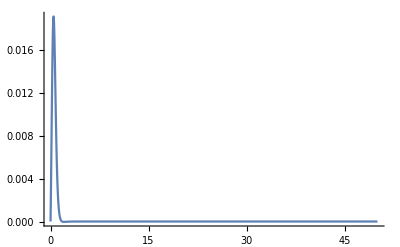

```mathematica
Plot[(rg1/.{θ->2}),{k3,0,50},PlotRange->All]
```

```mathematica
NIntegrate[ng1,{k3,2,∞},{θ,0,1},{y,-0.1,0.1}]
```

0.+2.05712×10^-6 ⅈ

```mathematica
NIntegrate[ng1,{k3,2,∞},{θ,1,2},{y,-0.1,0.1}]
NIntegrate[ng1,{k3,2,∞},{θ,2,π},{y,-0.1,0.1}]
NIntegrate[ng1,{k3,2,∞},{θ,π,4},{y,-0.1,0.1}]
NIntegrate[ng1,{k3,2,∞},{θ,4,5},{y,-0.1,0.1}]
NIntegrate[ng1,{k3,2,∞},{θ,5,2π},{y,-0.1,0.1}]
```

0.-3.26886×10^-7 ⅈ

0.+0.0000413484 ⅈ

0.+0.0000412071 ⅈ

0.-4.67809×10^-7 ⅈ

```mathematica
0.+0.0013155325867826467 ⅈ+0.+0.0006354490373185241 ⅈ+0.-0.001994060366548925 ⅈ+0.-0.0016685750321215062 ⅈ+0.-0.00001046208962868783 ⅈ+0.+0.001635959223231693 ⅈ+0.+2.057124879969735*^-6 ⅈ+0.-3.268856030925579*^-7 ⅈ+0.+0.00004134836712585943 ⅈ+0.+0.000041207144186875974 ⅈ+0.-4.6780880362268923*^-7 ⅈ+0.-4.6780880362268923*^-7 ⅈ
```

0.-2.80651×10^-6 ⅈ

```mathematica
Abs[0.-2.8065079838881352*^-6 ⅈ]
```

2.80651×10^-6